## Database Needs

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v2_9_11_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

## Data Extraction Functions

### General Data

```mathematica
Clear[Person];
Person=Association[{}];
```

```mathematica
getPerson[{id___Integer},{props__}]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="];
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
];
```

```mathematica
getPerson[{id___Integer},{props__},Time_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where (PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="]<>") and Time < "<>ToString[Time];
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

```mathematica
getPerson[{id___Integer},{props__},Time1_,Time2_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where (PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="]<>") and (Time > "<>ToString[Time1]<>" and Time < "<>ToString[Time2]<>")";
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

```mathematica
getPerson[{id___Integer},props:"Connections"]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonA, Time, PersonB FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>")";
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

```mathematica
getPerson[{id___Integer},props:"Connections",Time1_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonA, Time, PersonB FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>") and (Time > "<>ToString[Time1]<>")";
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

```mathematica
getPerson[{id___Integer},props:"Connections",Time1_,Time2_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonA, Time, PersonB FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>") and (Time > "<>ToString[Time1]<>" and Time < "<>ToString[Time2]<>")";
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

### Individual Data

```mathematica
extractPerson[id_,{props__}]:=Module[{},
Map[Thread[{Person[id]["Time"],Person[id][#]}]&,
{props}]
]
```

### Contact Network Functions

```mathematica
Clear[PersonConnections];
PersonConnections=Association[{}];
getConnections[{id___},Time_]:=Module[{query,rawData},
query="SELECT Time, PersonA, PersonB FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>") and Time < "<>ToString[Time];
rawData=SQLExecute[conn,query];
AppendTo[PersonConnections,Map[#->Cases[rawData,{t_,#,b_}:>{t,b}]&,{id}]]
]
getConnections[{id___},Time1_,Time2_]:=Module[{query,rawData},
query="SELECT Time, PersonA, PersonB FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>") and (Time > "<>ToString[Time1]<>" and Time < "<>ToString[Time2]<>")";
rawData=SQLExecute[conn,query];
AppendTo[PersonConnections,Map[#->Cases[rawData,{t_,#,b_}:>{t,b}]&,{id}]]
]
```

```mathematica
contactNet[n_]:=Tally[Person[#]["Age"][[-1]]&/@Select[PersonConnections[n][[All,2]],#<TotalPeople&]]
```

```mathematica
contactAgeNet[n_]:=Tally[Select[PersonConnections[n][[All,2]],#<TotalPeople&]]/.{{id_Integer,f_}:>{Person[n]["Age"][[-1]],Person[id]["Age"][[-1]],f}}
```

```mathematica
contactAgeNet[190]
```

Part::partd: Part specification Missing[KeyAbsent,190]⟦All,2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Tally::list: List expected at position 1 in Tally[Part[]].

Tally[Part[]]

### Graph

```mathematica
netConn[n_]:=Module[{connections},
connections= DeleteCases[Person[n]["Connections"],""];
If[MatchQ[connections,{}],Return[]];
DeleteDuplicates[Flatten[Map[UndirectedEdge[n,#]&,connections]]]]
```

## Plotting Functions

```mathematica
PopulationDataPlot[data_,opts___]:=ListLinePlot[data,
PlotStyle->{{Thick,SIRBlue},{Thick, SIRRed},{Thick, SIRGreen},{Thick, SIRBlack}},
PlotLegends->Placed[{"Susceptible","Infected","Recovered","Dead"},Above],
Frame->True,
FrameLabel->{Style["Time",Large],Style["Population",Large]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,
opts]
```

```mathematica
CellDataPlot[data_,opts___]:=ListLinePlot[data,
PlotStyle->{{Thick,SIRBlue},{Thick, SIRRed},{Thick, SIRGreen},{Thick, SIRBlack}},
PlotLegends->Placed[{"Susceptible Cells","Infected Cells","Viral Load"},Above],
Frame->True,
FrameLabel->{Style["Time",Large],Style["Cells",Large]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,
opts]
```

## Contact Network

### Connecting to Database

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v1_9_16_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

### Extract Data

```mathematica
TotalPeople=723;
StartTime =0;
EndTime =3000;
```

getPerson[Range[TotalPeople], {"Age", "State"}, StartTime, EndTime];
getConnections[Range[TotalPeople], StartTime, EndTime];

```mathematica
getPerson[Range[TotalPeople],{"Age","State"},EndTime];
```

```mathematica
getConnections[Range[TotalPeople],EndTime];
```

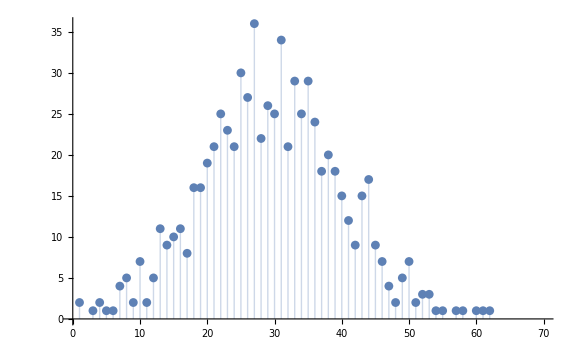

```mathematica
ListPlot[Map[Tooltip[{#[[1,1]],Length[#]},Labeled[Grid[Prepend[#/.{{_,id_Integer}:> {id,Person[id]["State"][[1]]}},{"ID","State"}],Frame->All],Grid[{{"Age",#[[1,1]]},{"Count",Length[#]}}],Top]]&,SortBy[GatherBy[Map[{Person[#]["Age"][[1]],#}&,Range[TotalPeople]],First],Last]],Filling->Axis,PlotRange->{{0,70},Full},ImageSize->Large]
```

```mathematica
ageConn=Flatten[contactAgeNet[#]&/@Range[TotalPeople],1];
```

ageConn = Join[ageConn, Map[{#, #, Max[ageConn[[All, -1]]]} &, Range[TotalPeople]]];

```mathematica
missingTerms=Complement[Tuples[Range[100],2],Cases[ageConn,{x_,y_,z_}:>{x,y}]]/.{{x_,y_}:> {x,y,0}};
```

```mathematica
ageConnM1=Join[ageConn,missingTerms];
```

```mathematica
ageConnM2 = ageConnM1/.{{x_,y_,z_}:>{y,x,z}};
```

```mathematica
cuttOffAge = 80;
```

```mathematica
ageConnM = Select[Map[{#[[1,1,1]],#[[1,1,2]],Total[#[[All,-1]]]}&,GatherBy[Join[ageConnM1/.{{x_,y_,z_}:> {{x,y},z}},ageConnM2/.{{x_,y_,z_}:> {{x,y},z}}],First]],((#[[1]]<cuttOffAge)&& (#[[2]]<cuttOffAge))&];
```

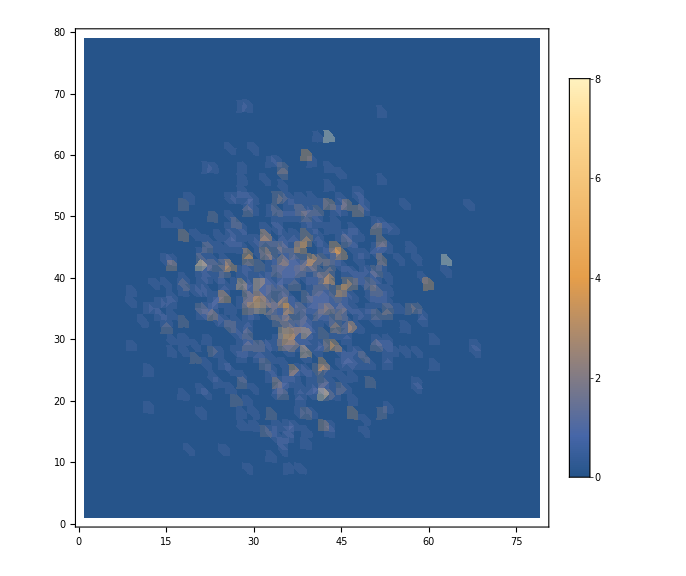

```mathematica
ListDensityPlot[ageConnM,ImageSize->Large,PlotLegends->Automatic,PlotRange->All]
```

## History Data

### Connect to Database

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v2_9_11_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

### Extract data

```mathematica
HistoryData=SQLSelect[conn,"HistoryData"];
```

HistoryData = SQLExecute[conn, "SELECT * FROM HistoryData WHERE Time < 36000"];

```mathematica
time= HistoryData[[All,2]];
sus=HistoryData[[All,3]];
exp=HistoryData[[All,4]];
inf=HistoryData[[All,5]];
rec=HistoryData[[All,6]];
ded=HistoryData[[All,7]];
nbn=HistoryData[[All,8]];
nif=HistoryData[[All,9]];
```

```mathematica
tsus=Thread[{time,sus}];
texp=Thread[{time,exp}];
tinf=Thread[{time,inf}];
trec=Thread[{time,rec}];
tded=Thread[{time,ded}];
tnbn=Thread[{time,nbn}];
tnif=Thread[{time,nif}];
```

```mathematica
{SIRBlue=RGBColor[0.2,0.2,0.7],SIRRed=RGBColor[0.7,0.2,0.2],SIRGreen=RGBColor[0.2,0.7,0.2],SIRBlack=RGBColor[0.,0.,0.]}
```

{RGBColor[0.2, 0.2, 0.7],RGBColor[0.7, 0.2, 0.2],RGBColor[0.2, 0.7, 0.2],RGBColor[0., 0., 0.]}

```mathematica
total =MapThread[{#1[[1]],Total[{#1[[2]],#2[[2]],#3[[2]],#4[[2]]}]}&,{tsus,tinf,trec,tded}];
```

```mathematica
d=Map[Total[#[[1;;-1;;1]]]&,DeleteCases[Split[tinf[[All,2]],#!=0&],{0}]];
```

```mathematica
computeProbability[data_]:=Module[{d,AllSizes,AllCounts,TotalProb,Probs},
d = SortBy[Tally[data],First];
AllSizes = d[[All,1]];
AllCounts=d[[All,2]];
TotalProb = Total[d/.{{s_Integer,n_Integer}:>s*n}];
Probs=Table[Total[d[[i;;-1]]/.{{s_Integer,n_Integer}:>s*n}]/TotalProb,{i,Length[AllCounts]}];
Thread[{Sort@AllSizes,Probs}]
];
pd=computeProbability[Rest[Sort[d]]];
line = Fit[Log@pd[[1;;Floor[0.8 Length[pd]]]], {1,x},x];
```

```mathematica
p=PopulationDataPlot[{tsus,tinf,trec,tded}];
i=ListPlot[d,
PlotStyle->{{Thick,SIRRed}},
PlotRange->Full,
Frame->True,
FrameLabel->{Style["Time",Large],Style["Epidemic Size",Large]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,PlotStyle->96,Filling->Axis];
h=Histogram[Rest[Sort[d]],100,ImageSize->Large,ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{Style["Epidemic Size",Bold,18],Style["Number of Occurance",Bold, 18]}];
l=Show[{
ListLogLogPlot[pd,
Joined->True, 
Mesh->All,
ImageSize->Large,
PlotRange->{Automatic,{Min[0.1,Min[pd]],1.1}},
Ticks->{Table[{10^k,Superscript[10,k]},{k,-2,5}],Table[{10^k,Superscript[10,k]},{k,-5,1,0.2}]},
GridLines->Automatic,
Frame->True,FrameLabel->{Style["Epidemic Size",Bold,18],Style["Number of Occurence",Bold, 18]}],
Plot[line,{x,0,pd[[-1,1]]},PlotRange->Full,PlotStyle->{Thick,Orange}]}
];
GraphicsGrid[{{p,i},{h,l}}]
```

-Graphics-

## Individual Data

```mathematica
getPerson[{2,3,4,5,6},{"SusCells","InfCells","VirLoads"},500,1500];
```

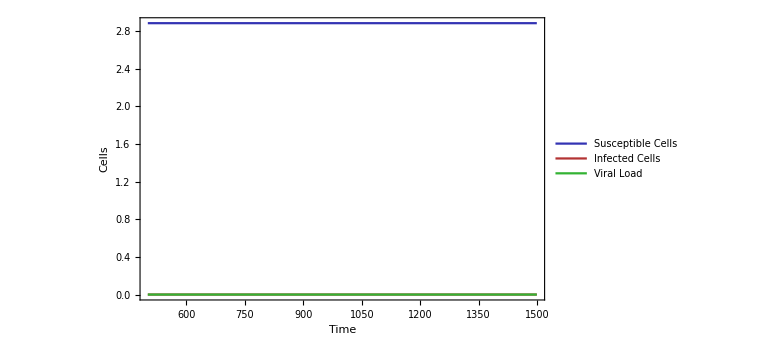

```mathematica
CellDataPlot[extractPerson[6,"SusCells","InfCells","VirLoads"]]
```

## Network

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v1_9_11_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
getPerson[Range[5],"Connections"];
```

```mathematica
g=DeleteCases[Flatten[Map[netConn[#]&,Range[5]]],Null];
```

```mathematica
Manipulate[
Module[{ghighlightsfrom,ghighlightsto,ghighlights,conlabels},
ghighlightsfrom = Cases[g,UndirectedEdge[hl,e_]:>Rule[hl,e]];
ghighlightsto = Cases[g,UndirectedEdge[e_,hl]:>Rule[e,hl]];
ghighlights=Join[ghighlightsfrom,ghighlightsto];
conlabels=Join[{hl->hl},#->#&/@ghighlightsfrom[[All,2]],#->#&/@ghighlightsto[[All,1]]];
Graph[g,VertexLabels->Switch[la,"Connected", conlabels, "All", "Name"],ImageSize->Large,VertexSize->Full,GraphHighlight->Prepend[ghighlights,hl],GraphHighlightStyle->"Thick",VertexLabelStyle->Directive[Red,Bold,18],GraphLayout->"CircularEmbedding"]
],
{{hl,1,"Node to highlight"},Range[5]},
{{la,"Connected","Label"},{"Connected","All"}}
]
```

```mathematica
N@GlobalClusteringCoefficient[g]
```

0.0209372